```mathematica
#!/usr/local/bin/MathematicaScript-script
```

```mathematica
graphlist = {};
singletonsgraphlist={};
singandhistgraphlist={};
singletonsNewList={};
singletonsHistoricalList={};
(*This indexlist represents how many frames are in the video, which we loop over to generate statistics for them all*)
(*it's important to change this value to an expression so It can be used as an expression, not a string*)
indexlist = Range[1, ToExpression[$ScriptCommandLine[[7]]]];
(*Set the name with an appropriate decription- this name will be reused over in the R file*)
name=$ScriptCommandLine[[3]];
resultsfilename = $ScriptCommandLine[[4]];
(*Set Directory to where the ./organelles.ce outputs are*)
toSetDirectory= ""<>ToString[$ScriptCommandLine[[2]]]<>""<>ToString[$ScriptCommandLine[[3]]]<>""
SetDirectory[toSetDirectory];
directory=$ScriptCommandLine[[2]];
(*Loop through the ./organelles.ce outputs*)
For[ k=1,k≤Length[indexlist],k++,
(*Read in historical adjacency matrix*)
l=ReadList[""<>ToString[directory]<>""<>ToString[name]<>"/"<>ToString[resultsfilename]<>"-"<>ToString[$ScriptCommandLine[[8]]]<>"-"<>ToString[indexlist[[k]]]<>".txt",{Number,Number}];
(*Uses each number pair from historical adjacency matrix as a directed then undirected graphs, storing each frames graph as g5*)
am=Table[l[[i]][[1]]->l[[i]][[2]],{i,1,Length[l]}];
  amf=Table[l[[i]][[1]]<->l[[i]][[2]],{i,1,Length[l]}];
  g5=Graph[amf,VertexStyle->Black];
(*Gathers all graphs as graphlist. Note:Graphlist is used to call the bC and Degree histograms from later.Accessed with graphlist[[n]]*)
graphlist = Append[graphlist,g5];

(*Read in frame specific singletons list (this one is historical)*)
singletons=ReadList[""<>ToString[directory]<>""<>ToString[name]<>"/"<>ToString[resultsfilename]<>"-"<>ToString[$ScriptCommandLine[[8]]]<>"-"<>ToString[indexlist[[k]]]<>"-single.txt",Number];
(*Lets also collect a list of the number of historical singletons collected over time*)
singletonsHistoricalList=Append[singletonsHistoricalList,Length[singletons]];

(*Read in frame specific singletons list (this one is for any new singletons in the current frame)*)
singletonNew=ReadList[""<>ToString[directory]<>""<>ToString[name]<>"/"<>ToString[resultsfilename]<>"-"<>ToString[$ScriptCommandLine[[8]]]<>"-"<>ToString[indexlist[[k]]]<>"-single-new.txt",Number];
(*For these we won't do anything else with them, so can just take how many novel singletons there are and make a list of them to export asfter leaving the loop*)
singletonsNewList=Append[singletonsNewList,Length[singletonNew]];
(*could just take vertex number from the length of the singletons lists being imported. But we may also want to access the ids for these singleton mitochondria, so we will store them in these graphs generations. Storing as a graph also simplifies social network stat extractions*)
(*Makes a graph of singleton mitochondria, labelled by id, stores these networks in a list. Accessed with singletonsGraphList[[n]] *)
singletonsGraph=Graph[singletons,{},VertexLabels->"Name"];
singletonsgraphlist=Append[singletonsgraphlist,singletonsGraph];
(*writes singletons nodes into an adjacency matrix- they have edges linking themslves. Ie 1<->1. Therefore you cannot use these for edge counts but can for degree calc, betweeness calc and node number.*)
sng=Transpose[{singletons,singletons}];
sngam=Table[sng[[i]][[1]]->sng[[i]][[2]],{i,1,Length[sng]}];
  sngamf=Table[sng[[i]][[1]]<->sng[[i]][[2]],{i,1,Length[sng]}];
(*joins historic adjacency matrix to the singletons matrix. You can't put single non connected nodes into graphs, unless they are all non connected. So, I've joined the adjacency matrix where the singletons are connected to themselves to the original historical network.*)
historicandsingletonsgraph=Graph[Join[amf,sngamf]];
singandhistgraphlist=Append[singandhistgraphlist,historicandsingletonsgraph];
(*While still working with each g5, export normalised BC as it needs the vertexnumber at that exact g5 for the calculation, and export just that network graph, and BC and Degree Hists for reference*)
(*Export[""<>ToString[indexlist[[k]]]<>"_normalisedBC.csv",BetweennessCentrality[graphlist[[k]]]*2/((VertexCount[graphlist[[k]]]-1)*(VertexCount[graphlist[[k]]]-2))];
Export[""<>ToString[indexlist[[k]]]<>"_maxnormalisedBC.csv",Max[BetweennessCentrality[graphlist[[k]]]]*2/((VertexCount[graphlist[[k]]]-1)*(VertexCount[graphlist[[k]]]-2))];
Export[""<>ToString[indexlist[[k]]]<>"_meannormalisedBC.csv",Mean[BetweennessCentrality[graphlist[[k]]]]*2/((VertexCount[graphlist[[k]]]-1)*(VertexCount[graphlist[[k]]]-2))];
*)
(* with singletons *)
(*Export[""<>ToString[indexlist[[k]]]<>"_normalisedBC_WS.csv",BetweennessCentrality[singandhistgraphlist[[k]]]*2/((VertexCount[singandhistgraphlist[[k]]]-1)*(VertexCount[singandhistgraphlist[[k]]]-2))];
Export[""<>ToString[indexlist[[k]]]<>"_maxnormalisedBC_WS.csv",Max[BetweennessCentrality[singandhistgraphlist[[k]]]]*2/((VertexCount[singandhistgraphlist[[k]]]-1)*(VertexCount[singandhistgraphlist[[k]]]-2))];
Export[""<>ToString[indexlist[[k]]]<>"_meannormalisedBC_WS.csv",Mean[BetweennessCentrality[singandhistgraphlist[[k]]]]*2/((VertexCount[singandhistgraphlist[[k]]]-1)*(VertexCount[singandhistgraphlist[[k]]]-2))];
*)
(*Export["Results"<>ToString[name]<>"Frame"<>ToString[indexlist[[k]]]<>".jpg",g5];
Export["Results"<>ToString[name]<>"Frame"<>ToString[indexlist[[k]]]<>"DegreeHist.jpg",Histogram[DegreeCentrality[g5]]];
Export["Results"<>ToString[name]<>"Frame"<>ToString[indexlist[[k]]]<>"BCHist.jpg",Histogram[BetweennessCentrality[g5]]];*)
Print["Results"<>ToString[name]<>"Frame"<>ToString[indexlist[[k]]]<>"done"]
]


(*LETS also get the average distance over the network out for networks with singletons *)
(*THIS way adds a bunch of 0s, as the singleton is 0 distance from itself. But, each node in the connected netwrok also produces a distance to itself of 0. So, its hard to distinguish from singletons and connected nodes in that respect. So what we'll do instead is take the distance across the network for the without-singletons graph and divide it by the number of distances plus the number of singletons at that point in time*)
averagedistlistnoinfWS={};
For[k=1,k≤Length[indexlist],k++,
Print["av dist Frame",ToString[k],""];
(*Find the average of distances across the network in each frame.Remove Infinities as Thats the distance found between 2 connected components. Also remove 0s thats the distance between a node and itself.*)averagedistlist=GraphDistanceMatrix[graphlist[[k]]];
removedInf=DeleteCases[Flatten[averagedistlist],∞];
removed0=DeleteCases[removedInf,0];
averagedistWS=N[Total[removed0]/(Length[removed0]+singletonsHistoricalList[[k]])];
averagedistlistnoinfWS=Append[averagedistlistnoinfWS,averagedistWS];
]


(*Stores Summary Statistic outputs as various lists, which then need transposing and prepending with column names*)
FrameList= indexlist;
numberccWS = Length/@ConnectedComponents/@singandhistgraphlist;
numbercc = Length/@ConnectedComponents/@graphlist;
(* Map is concerned about using level {2} to track length of the seprate cc, but level {1} reads lengths of whole CCs, giving numbercc ranther than length cc- level 2 dives one step deeper to give the output we want*)
sizes=Map[Length,ConnectedComponents/@graphlist,{2}];
sizesreformat=Map[Length,ConnectedComponents/@graphlist,{2}];
sizesWS=Map[Length,ConnectedComponents/@singandhistgraphlist,{2}];
sizesreformatWS=Map[Length,ConnectedComponents/@singandhistgraphlist,{2}];
(*Edge number should be the same, whether using graph with singletons or not. Edges are only between CONNECXTED nodes, not singles. We don't want to include self-associated edges. Therefore this edges_WS is just an insurance and a proof of point.*)
edgesWS =(EdgeCount/@singletonsGraphList)+(EdgeCount/@graphlist);
edges =EdgeCount/@graphlist;
vertices =VertexCount/@graphlist;
verticesWS=(VertexCount/@singletonsGraphList)+(VertexCount/@graphlist);
BCWS= BetweennessCentrality/@singandhistgraphlist;
BC= BetweennessCentrality/@graphlist;
(*We're using DegreeCentrality not VErtexDegree as VertexDegree identifies self associated nodes as having a degree of 2, which is not in line with our definiton of degree for singletons. DegreeCentrality nopminates self-associated as degree = 0*)
Degree1WS= DegreeCentrality/@singandhistgraphlist;
Degree1= DegreeCentrality/@graphlist;
MeanDegreeWS=Flatten[{Map[Mean,DegreeCentrality/@singandhistgraphlist]}] ;
MeanDegree=Flatten[{Map[Mean,DegreeCentrality/@graphlist]}] ;
MeanDegreeWS=N[MeanDegreeWS];
MeanDegree=N[MeanDegree];
SDDegreeWS=Flatten[{Map[StandardDeviation,DegreeCentrality/@singandhistgraphlist]}] ;
SDDegree=Flatten[{Map[StandardDeviation,DegreeCentrality/@graphlist]}] ;
SDDegreeWS=N[SDDegreeWS];
SDDegree=N[SDDegree];
CoeffVarDegreeWS=SDDegreeWS/MeanDegreeWS;
CoeffVarDegree=SDDegree/MeanDegree;
MaxDegreeWS=Flatten[{Map[Max,DegreeCentrality/@singandhistgraphlist]}];
MaxDegree=Flatten[{Map[Max,DegreeCentrality/@graphlist]}];
MeanBCWS=Flatten[{Map[Mean,BetweennessCentrality/@singandhistgraphlist]}];
MeanBC=Flatten[{Map[Mean,BetweennessCentrality/@graphlist]}];
MaxBCWS=Flatten[{Map[Max,BetweennessCentrality/@singandhistgraphlist]}];
MaxBC=Flatten[{Map[Max,BetweennessCentrality/@graphlist]}];

(*Exports for singletons lists*)
Export[""<>ToString[name]<>"_CC_WS.csv",Prepend[Transpose@{FrameList,numberccWS},{"Frame","No of CC"}]];
Export[""<>ToString[name]<>"_EN_WS.csv",Prepend[Transpose@{FrameList,edgesWS},{"Frame","Edges"}]];
Export[""<>ToString[name]<>"_NN_WS.csv",Prepend[Transpose@{FrameList,verticesWS},{"Frame","Nodes"}]];
Export[""<>ToString[name]<>"_SCC_WS.csv",Prepend[Transpose@{FrameList,sizesWS},{"Frame","V1"}]];
Export[""<>ToString[name]<>"_SCCreformat2_WS.csv",sizesreformatWS];
Export[""<>ToString[name]<>"_BC_WS.csv",Prepend[Transpose@{BCWS},{"V1"}]];
Export[""<>ToString[name]<>"_D_WS.csv",Prepend[Transpose@{Degree1WS},{"V1"}]];
Export[""<>ToString[name]<>"_MaxD_WS.csv",Prepend[Transpose@{FrameList,MaxDegreeWS},{"Frame","Max Degree"}]];
Export[""<>ToString[name]<>"_MaxBC_WS.csv",Prepend[Transpose@{FrameList,MaxBCWS},{"Frame","Max Betweeness Centrality"}]];
Export[""<>ToString[name]<>"_MeanD_WS.csv",Prepend[Transpose@{FrameList,MeanDegreeWS},{"Frame","Mean Degree"}]];
Export[""<>ToString[name]<>"_SdD_WS.csv",Prepend[Transpose@{FrameList,SDDegreeWS},{"Frame","SD Degree"}]];
Export[""<>ToString[name]<>"_CoeffVarD_WS.csv",Prepend[Transpose@{FrameList,CoeffVarDegreeWS},{"Frame","CoeffVarD"}]];
Export[""<>ToString[name]<>"_MeanBC_WS.csv",Prepend[Transpose@{FrameList,MeanBCWS},{"Frame","Mean Betweeness Centrality"}]];
Export[""<>ToString[name]<>"_F.csv",Prepend[Transpose@{FrameList},{"Frame"}]];
Export[""<>ToString[name]<>"_singletons-new-count.csv",Prepend[Transpose@{FrameList,singletonsNewList},{"Frame","New singletons in each frame"}]];
Export[""<>ToString[name]<>"_singletons-historical-count.csv",Prepend[Transpose@{FrameList,singletonsHistoricalList},{"Frame","Historical singletons count over time"}]];
Export["averageDistsOverNetworksForAllFrames_WS.csv",Prepend[Transpose@{Flatten[indexlist],Flatten[averagedistlistnoinfWS]},{"Frames","Distance between all nodes, av by nodes+singletons"}]]
(*Export the desired histograms and joined listsfor historic adjacency matrix. BC and Degree are very long lists of lists, so are exported on their own then joined later in R to the framelist*)
(*Export[""<>ToString[name]<>"_CC.csv",Prepend[Transpose@{FrameList,numbercc},{"Frame","No of CC"}]];
Export[""<>ToString[name]<>"_EN.csv",Prepend[Transpose@{FrameList,edges},{"Frame","Edges"}]];
Export[""<>ToString[name]<>"_NN.csv",Prepend[Transpose@{FrameList,vertices},{"Frame","Nodes"}]];
Export[""<>ToString[name]<>"_SCC.csv",Prepend[Transpose@{FrameList,sizes},{"Frame","V1"}]];
Export[""<>ToString[name]<>"_SCCreformat2.csv",sizesreformat];
Export[""<>ToString[name]<>"_BC.csv",Prepend[Transpose@{BC},{"V1"}]];
Export[""<>ToString[name]<>"_D.csv",Prepend[Transpose@{Degree1},{"V1"}]];
Export[""<>ToString[name]<>"_MaxD.csv",Prepend[Transpose@{FrameList,MaxDegree},{"Frame","Max Degree"}]];
Export[""<>ToString[name]<>"_MaxBC.csv",Prepend[Transpose@{FrameList,MaxBC},{"Frame","Max Betweeness Centrality"}]];
Export[""<>ToString[name]<>"_MeanD.csv",Prepend[Transpose@{FrameList,MeanDegree},{"Frame","Mean Degree"}]];
Export[""<>ToString[name]<>"_SdD.csv",Prepend[Transpose@{FrameList,SDDegree},{"Frame","SD Degree"}]];
Export[""<>ToString[name]<>"_CoeffVarD.csv",Prepend[Transpose@{FrameList,CoeffVarDegree},{"Frame","CoeffVarD"}]];
Export[""<>ToString[name]<>"_MeanBC.csv",Prepend[Transpose@{FrameList,MeanBC},{"Frame","Mean Betweeness Centrality"}]];
Export[""<>ToString[name]<>"_F.csv",Prepend[Transpose@{FrameList},{"Frame"}]];*)

Print["SummaryStatsExported"]
(*Input the number of frames, it's important to change this value to an expression so It can be used as an expression, not a string*)
frameno=ToExpression[$ScriptCommandLine[[7]]]
(*This step take the number of frames you have, and divides it into 11+1 equally spaced values, rounded to the nearest whole number*)
frameSteps=Round[Subdivide[1,frameno,11],1]
(*Re-load the files we've just generated to be the frames specified by the equal division of frame number into 11 intervals*)
graphic1=Import["Results"<>ToString[name]<>"Frame"<>ToString[frameSteps[[1]]]<>".jpg"];
graphic2= Import["Results"<>ToString[name]<>"Frame"<>ToString[frameSteps[[2]]]<>".jpg"];
graphic3= Import["Results"<>ToString[name]<>"Frame"<>ToString[frameSteps[[3]]]<>".jpg"];
graphic4= Import["Results"<>ToString[name]<>"Frame"<>ToString[frameSteps[[4]]]<>".jpg"];
graphic5= Import["Results"<>ToString[name]<>"Frame"<>ToString[frameSteps[[5]]]<>".jpg"];
graphic6= Import["Results"<>ToString[name]<>"Frame"<>ToString[frameSteps[[6]]]<>".jpg"];
graphic7= Import["Results"<>ToString[name]<>"Frame"<>ToString[frameSteps[[7]]]<>".jpg"];
graphic8= Import["Results"<>ToString[name]<>"Frame"<>ToString[frameSteps[[8]]]<>".jpg"];
graphic9= Import["Results"<>ToString[name]<>"Frame"<>ToString[frameSteps[[9]]]<>".jpg"];
graphic10= Import["Results"<>ToString[name]<>"Frame"<>ToString[frameSteps[[10]]]<>".jpg"];
graphic11= Import["Results"<>ToString[name]<>"Frame"<>ToString[frameSteps[[11]]]<>".jpg"];
graphic12= Import["Results"<>ToString[name]<>"Frame"<>ToString[frameSteps[[12]]]<>".jpg"];
(*Export these into a neat grid shape of networks- handy for quick visualisation*)
Export[""<>ToString[name]<>"_AllNetworks.jpg",Grid[{{"Frame"<>ToString[frameSteps[[1]]]<>"", "Frame"<>ToString[frameSteps[[2]]]<>"", "Frame"<>ToString[frameSteps[[3]]]<>""},{graphic1,graphic2,graphic3},{"Frame"<>ToString[frameSteps[[4]]]<>"", "Frame"<>ToString[frameSteps[[5]]]<>"","Frame"<>ToString[frameSteps[[6]]]<>""},{graphic4,graphic5,graphic6},{"Frame"<>ToString[frameSteps[[7]]]<>"", "Frame"<>ToString[frameSteps[[8]]]<>"", "Frame"<>ToString[frameSteps[[9]]]<>""},{graphic7,graphic8,graphic9},
{"Frame"<>ToString[frameSteps[[10]]]<>"", "Frame"<>ToString[frameSteps[[11]]]<>"", "Frame"<>ToString[frameSteps[[12]]]<>""},{graphic10,graphic11,graphic12}}]];
Print["NetworkImageGridExported"]
```

/home/gadmin/Documents/Joanna/neaterAnalysisPipeline/MitoGFP/ScaleAndCrop-bigcellmanymitos

ResultsScaleAndCrop-bigcellmanymitosFrame1done

ResultsScaleAndCrop-bigcellmanymitosFrame2done

ResultsScaleAndCrop-bigcellmanymitosFrame3done

ResultsScaleAndCrop-bigcellmanymitosFrame4done

ResultsScaleAndCrop-bigcellmanymitosFrame5done

ResultsScaleAndCrop-bigcellmanymitosFrame6done

ResultsScaleAndCrop-bigcellmanymitosFrame7done

ResultsScaleAndCrop-bigcellmanymitosFrame8done

ResultsScaleAndCrop-bigcellmanymitosFrame9done

ResultsScaleAndCrop-bigcellmanymitosFrame10done

ResultsScaleAndCrop-bigcellmanymitosFrame11done

ResultsScaleAndCrop-bigcellmanymitosFrame12done

ResultsScaleAndCrop-bigcellmanymitosFrame13done

ResultsScaleAndCrop-bigcellmanymitosFrame14done

ResultsScaleAndCrop-bigcellmanymitosFrame15done

ResultsScaleAndCrop-bigcellmanymitosFrame16done

ResultsScaleAndCrop-bigcellmanymitosFrame17done

ResultsScaleAndCrop-bigcellmanymitosFrame18done

ResultsScaleAndCrop-bigcellmanymitosFrame19done

ResultsScaleAndCrop-bigcellmanymitosFrame20done

ResultsScaleAndCrop-bigcellmanymitosFrame21done

ResultsScaleAndCrop-bigcellmanymitosFrame22done

ResultsScaleAndCrop-bigcellmanymitosFrame23done

ResultsScaleAndCrop-bigcellmanymitosFrame24done

ResultsScaleAndCrop-bigcellmanymitosFrame25done

ResultsScaleAndCrop-bigcellmanymitosFrame26done

ResultsScaleAndCrop-bigcellmanymitosFrame27done

ResultsScaleAndCrop-bigcellmanymitosFrame28done

ResultsScaleAndCrop-bigcellmanymitosFrame29done

ResultsScaleAndCrop-bigcellmanymitosFrame30done

ResultsScaleAndCrop-bigcellmanymitosFrame31done

ResultsScaleAndCrop-bigcellmanymitosFrame32done

ResultsScaleAndCrop-bigcellmanymitosFrame33done

ResultsScaleAndCrop-bigcellmanymitosFrame34done

ResultsScaleAndCrop-bigcellmanymitosFrame35done

ResultsScaleAndCrop-bigcellmanymitosFrame36done

ResultsScaleAndCrop-bigcellmanymitosFrame37done

ResultsScaleAndCrop-bigcellmanymitosFrame38done

ResultsScaleAndCrop-bigcellmanymitosFrame39done

ResultsScaleAndCrop-bigcellmanymitosFrame40done

ResultsScaleAndCrop-bigcellmanymitosFrame41done

ResultsScaleAndCrop-bigcellmanymitosFrame42done

ResultsScaleAndCrop-bigcellmanymitosFrame43done

ResultsScaleAndCrop-bigcellmanymitosFrame44done

ResultsScaleAndCrop-bigcellmanymitosFrame45done

ResultsScaleAndCrop-bigcellmanymitosFrame46done

ResultsScaleAndCrop-bigcellmanymitosFrame47done

ResultsScaleAndCrop-bigcellmanymitosFrame48done

ResultsScaleAndCrop-bigcellmanymitosFrame49done

ResultsScaleAndCrop-bigcellmanymitosFrame50done

ResultsScaleAndCrop-bigcellmanymitosFrame51done

ResultsScaleAndCrop-bigcellmanymitosFrame52done

ResultsScaleAndCrop-bigcellmanymitosFrame53done

ResultsScaleAndCrop-bigcellmanymitosFrame54done

ResultsScaleAndCrop-bigcellmanymitosFrame55done

ResultsScaleAndCrop-bigcellmanymitosFrame56done

ResultsScaleAndCrop-bigcellmanymitosFrame57done

ResultsScaleAndCrop-bigcellmanymitosFrame58done

ResultsScaleAndCrop-bigcellmanymitosFrame59done

ResultsScaleAndCrop-bigcellmanymitosFrame60done

ResultsScaleAndCrop-bigcellmanymitosFrame61done

ResultsScaleAndCrop-bigcellmanymitosFrame62done

ResultsScaleAndCrop-bigcellmanymitosFrame63done

ResultsScaleAndCrop-bigcellmanymitosFrame64done

ResultsScaleAndCrop-bigcellmanymitosFrame65done

ResultsScaleAndCrop-bigcellmanymitosFrame66done

ResultsScaleAndCrop-bigcellmanymitosFrame67done

ResultsScaleAndCrop-bigcellmanymitosFrame68done

ResultsScaleAndCrop-bigcellmanymitosFrame69done

ResultsScaleAndCrop-bigcellmanymitosFrame70done

ResultsScaleAndCrop-bigcellmanymitosFrame71done

ResultsScaleAndCrop-bigcellmanymitosFrame72done

ResultsScaleAndCrop-bigcellmanymitosFrame73done

ResultsScaleAndCrop-bigcellmanymitosFrame74done

ResultsScaleAndCrop-bigcellmanymitosFrame75done

ResultsScaleAndCrop-bigcellmanymitosFrame76done

ResultsScaleAndCrop-bigcellmanymitosFrame77done

ResultsScaleAndCrop-bigcellmanymitosFrame78done

ResultsScaleAndCrop-bigcellmanymitosFrame79done

ResultsScaleAndCrop-bigcellmanymitosFrame80done

ResultsScaleAndCrop-bigcellmanymitosFrame81done

ResultsScaleAndCrop-bigcellmanymitosFrame82done

ResultsScaleAndCrop-bigcellmanymitosFrame83done

ResultsScaleAndCrop-bigcellmanymitosFrame84done

ResultsScaleAndCrop-bigcellmanymitosFrame85done

ResultsScaleAndCrop-bigcellmanymitosFrame86done

ResultsScaleAndCrop-bigcellmanymitosFrame87done

ResultsScaleAndCrop-bigcellmanymitosFrame88done

ResultsScaleAndCrop-bigcellmanymitosFrame89done

ResultsScaleAndCrop-bigcellmanymitosFrame90done

ResultsScaleAndCrop-bigcellmanymitosFrame91done

ResultsScaleAndCrop-bigcellmanymitosFrame92done

ResultsScaleAndCrop-bigcellmanymitosFrame93done

ResultsScaleAndCrop-bigcellmanymitosFrame94done

ResultsScaleAndCrop-bigcellmanymitosFrame95done

ResultsScaleAndCrop-bigcellmanymitosFrame96done

ResultsScaleAndCrop-bigcellmanymitosFrame97done

ResultsScaleAndCrop-bigcellmanymitosFrame98done

ResultsScaleAndCrop-bigcellmanymitosFrame99done

ResultsScaleAndCrop-bigcellmanymitosFrame100done

ResultsScaleAndCrop-bigcellmanymitosFrame101done

ResultsScaleAndCrop-bigcellmanymitosFrame102done

ResultsScaleAndCrop-bigcellmanymitosFrame103done

ResultsScaleAndCrop-bigcellmanymitosFrame104done

ResultsScaleAndCrop-bigcellmanymitosFrame105done

ResultsScaleAndCrop-bigcellmanymitosFrame106done

ResultsScaleAndCrop-bigcellmanymitosFrame107done

ResultsScaleAndCrop-bigcellmanymitosFrame108done

ResultsScaleAndCrop-bigcellmanymitosFrame109done

ResultsScaleAndCrop-bigcellmanymitosFrame110done

ResultsScaleAndCrop-bigcellmanymitosFrame111done

ResultsScaleAndCrop-bigcellmanymitosFrame112done

ResultsScaleAndCrop-bigcellmanymitosFrame113done

ResultsScaleAndCrop-bigcellmanymitosFrame114done

ResultsScaleAndCrop-bigcellmanymitosFrame115done

ResultsScaleAndCrop-bigcellmanymitosFrame116done

ResultsScaleAndCrop-bigcellmanymitosFrame117done

ResultsScaleAndCrop-bigcellmanymitosFrame118done

{0.512397,0.707692,0.970588,1.06294,1.14667,1.18471,1.26061,1.37209,1.52174,1.58763,1.67164,1.84906,1.92857,1.93103,1.95918,2.03906,2.02222,2.03571,2.11847,2.17568,2.23026,2.24127,2.27077,2.28402,2.32571,2.35655,2.39024,2.39791,2.39594,2.40299,2.42788,2.45238,2.46651,2.46085,2.47162,2.46512,2.47107,2.48276,2.46275,2.45124,2.46442,2.47059,2.48014,2.47535,2.49741,2.52525,2.5082,2.50637,2.53978,2.54211,2.56364,2.59675,2.62409,2.61648,2.61304,2.62912,2.63158,2.62698,2.6502,2.66496,2.66083,2.64461,2.64346,2.65089,2.65111,2.65829,2.69388,2.70917,2.6989,2.69848,2.7103,2.71111,2.72461,2.71737,2.71862,2.72946,2.73248,2.75048,2.76527,2.79736,2.80336,2.80517,2.81061,2.82236,2.82248,2.81938,2.83656,2.83681,2.84464,2.84792,2.84757,2.85453,2.8602,2.86341,2.86543,2.8752,2.87362,2.87618,2.87199,2.87077,2.87976,2.88266,2.87809,2.87361,2.88059,2.8966,2.90922,2.91501,2.92621,2.92768,2.92435,2.93306,2.94293,2.93531,2.94055,2.95421,2.95995,2.97653}

{1.29167,1.48387,1.76,1.85366,1.91111,1.9375,1.96226,2.0885,2.17054,2.26471,2.3662,2.54545,2.57143,2.57471,2.58065,2.66327,2.66341,2.68868,2.75113,2.74043,2.77869,2.81275,2.8716,2.89139,2.90714,2.91724,2.93023,2.9359,2.96855,2.97231,2.95322,2.9683,2.97493,2.94118,2.95561,2.9821,2.96774,3.00737,3.01923,3.03791,3.0463,3.03386,3.02643,3.04989,3.05708,3.0303,3.04781,3.05039,3.04869,3.04587,3.05967,3.07343,3.0906,3.10624,3.11405,3.12235,3.13002,3.14739,3.17941,3.21109,3.19699,3.19231,3.1913,3.19544,3.1955,3.18194,3.19785,3.2037,3.20209,3.18974,3.18537,3.19054,3.19656,3.18554,3.19382,3.20471,3.21487,3.21356,3.23438,3.24726,3.25894,3.25966,3.26115,3.28092,3.28557,3.28542,3.30061,3.30769,3.30409,3.31225,3.30418,3.30829,3.31238,3.31326,3.31716,3.32778,3.32845,3.32729,3.32914,3.32917,3.33686,3.34035,3.34609,3.34021,3.34638,3.34112,3.35255,3.36549,3.35266,3.36262,3.36392,3.36257,3.37121,3.37152,3.37318,3.38813,3.39714,3.41001}

SummaryStatsExported

118

{4,48,88,132,176,216,260,300,344,388,428,472}


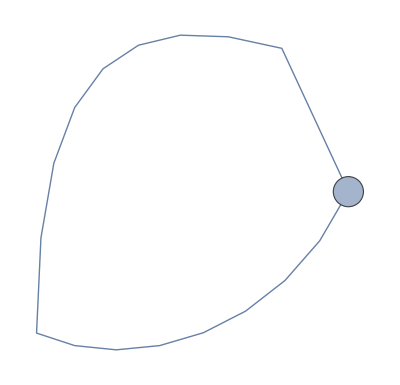
graph | betweeness | degree | 
-Graphics- | {0.} | {0} | 0
-Graphics- | {0.} | {0} | 1

```mathematica
Grid[{{"graph","betweeness","degree","edge count"},{a=Graph[Range[1],{}],BetweennessCentrality[a],DegreeCentrality[a],EdgeCount[a]},{b=Graph[{1<->1}],BetweennessCentrality[b],DegreeCentrality[b],EdgeCount[b]}}]
```

```mathematica
DegreeCentrality
```

```mathematica
x=Transpose[{singletons,singletons}]
```

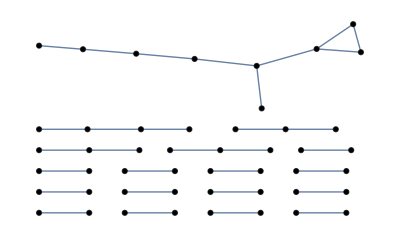

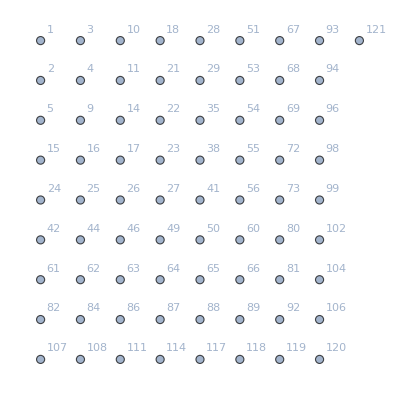

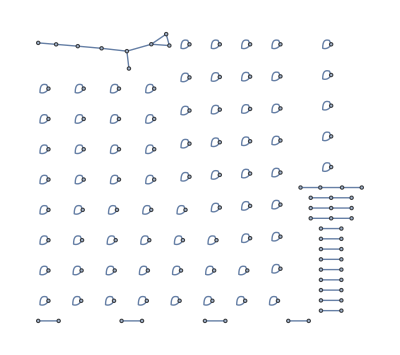

```mathematica
graphlist[[1]]
singletonsgraphlist[[1]]
singandhistgraphlist[[1]]
```

```mathematica
singandhistgraphlist[[1]]
```

-Graphics-

```mathematica
DegreeCentrality[singandhistgraphlist[[1]]]
```

{1,2,1,1,1,1,1,1,2,1,2,3,2,2,1,2,2,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,3,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
VertexDegree[singandhistgraphlist[[1]]]
```

{1,2,1,1,1,1,1,1,2,1,2,3,2,2,1,2,2,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,3,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
DegreeCentrality[Graph[{1<->2}]]
```

{1,1}

```mathematica
VertexDegree[Graph[{1<->2}]]
```

{1,1}